## Waveforms of a Binary System and a Lagrange Three-body System

```mathematica
(*cleanup the kernel*)
Remove["Global`*"]
```

### Without Radiation Reaction

First, we define the functions for the chirp mass, initial phase, separation distance, and the frequency.

```mathematica
(*quantities derivable from the source parameters*)
(*α, β, and γ are the masses of the bodies while l is the initial separation of the masses*)
Subscript[M, chirp][α_,β_,γ_]:=(α+β+γ)^(-1/5)(1/2×((α)^2(β-γ)^2+(β)^2(γ-α)^2+(γ)^2(α-β)^2)/(α β+β γ+γ α))^(3/5);
Subscript[Ψ, quad][α_,β_,γ_]:=ArcTan[(√3 α(β-γ))/(α(β+γ)-2β γ)];
Subscript[Ψ, 1][α_,β_,γ_]:=ArcTan[-((β-γ)((α-β)(α-γ)-3β γ))/(√3 α(β(β-α)+γ(γ-α)))];
Subscript[Ψ, 3][α_,β_,γ_]:=ArcTan[((α-β)(β-γ)(γ-α))/(3 √3 α β γ)];
coal[l_,α_,β_,γ_]:=(5 l^4)/(256(α+β+γ)^(4/3)(Subscript[M, chirp][α,β,γ])^(5/3));

a[l_,α_,β_,γ_,t_]:=l(1-t/coal[l,α,β,γ])^(1/4);
ω[l_,α_,β_,γ_,t_]:=(α+β+γ)^(1/2)/l^(3/2)(1-t/coal[l,α,β,γ])^(-3/8);
```

Without radiation reaction, we have the following waveforms.

```mathematica
(*mass quadrupole without radiation reaction*)
Subscript[h, quadplus][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-2/r(α+β+γ)^(5/6)(Subscript[M, chirp][α,β,γ])^(5/6)((α+β+γ)^(1/2)/l^(3/2))^(2/3)(1+Cos[ι]^2)(√(α β+β γ +γ α))/(α+β+γ)Cos[2((α+β+γ)^(1/2)/l^(3/2)) t-Subscript[Ψ, quad][α,β,γ]-ϕ]; 
Subscript[h, quadcross][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-2/r(α+β+γ)^(5/6)(Subscript[M, chirp][α,β,γ])^(5/6)((α+β+γ)^(1/2)/l^(3/2))^(2/3)Cos[ι](√(α β+β γ +γ α))/(α+β+γ)Sin[2(α+β+γ)^(1/2)/l^(3/2) t-Subscript[Ψ, quad][α,β,γ]-ϕ]; 
(*mass octupole + current quadrupole times without radiation reaction*)
Subscript[h, octcqPlus][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-1/(4 r)(α+β+γ)^2((α+β+γ)^(1/2)/l^(3/2)) Sin[ι](9(1+Cos[ι]^2)(√(27 α^2 β^2 γ^2+(α-β)^2(β-γ)^2(α-γ)^2))/(α+β+γ)^3 Cos[3((α+β+γ)^(1/2)/l^(3/2))t-Subscript[Ψ, 3][α,β,γ]-3ϕ]-1/2(5+Cos[ι]^2)(√(3 α^2(β(β-α)+γ(γ-α))^2+(β-γ)^2((α-β)(α-γ)-3β γ)^2))/(α+β+γ)^3 Cos[((α+β+γ)^(1/2)/l^(3/2))t-Subscript[Ψ, 1][α,β,γ]-ϕ])
Subscript[h, octcqCross][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-1/(4 r)(α+β+γ)^2((α+β+γ)^(1/2)/l^(3/2)) Sin[2ι](9(3 √3 (α β γ)/(α+β+γ)^3 Sin[3((α+β+γ)^(1/2)/l^(3/2)) t-3ϕ]-((α-β)(β-γ)(γ-α))/(α+β+γ)^3 Cos[3((α+β+γ)^(1/2)/l^(3/2)) t-3ϕ])-3((√3)/2 α/(α+β+γ)^3(β(β-α)+γ(γ-α))Sin[((α+β+γ)^(1/2)/l^(3/2)) t-ϕ]+1/2(β-γ)/(α+β+γ)^3((α-β)(α-γ)-3β γ)Cos[((α+β+γ)^(1/2)/l^(3/2)) t-ϕ]))
Subscript[h, octcqPlusTwoBody][l_,α_,β_,r_,ι_,t_,ϕ_]:=1/(4r) (α β(β-α))/(α+β)((α+β)^(1/2)/l^(3/2))Sin[ι]((Cos[ι]^2+5)Cos[((α+β)^(1/2)/l^(3/2))t+ϕ]-9(1+Cos[ι]^2)Cos[3((α+β)^(1/2)/l^(3/2))t+3ϕ]);
Subscript[h, octcqCrossTwoBody][l_,α_,β_,r_,ι_,t_,ϕ_]:=3/(4r) (α β(β-α))/(α+β)((α+β)^(1/2)/l^(3/2))Sin[2ι](Sin[((α+β)^(1/2)/l^(3/2))t+3ϕ]-3Sin[3((α+β)^(1/2)/l^(3/2))t+ϕ]);
Subscript[h, combinedPlusTwoBody][l_,α_,β_,r_,ι_,t_,ϕ_]:=Subscript[h, quadplus][l,0,α,β,r,ι,t,ϕ]+Subscript[h, octcqPlusTwoBody][l,α,β,r,ι,t,ϕ];
Subscript[h, combinedPlusThreeBody][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=Subscript[h, quadplus][l,α,β,γ,r,ι,t,ϕ]+Subscript[h, octcqPlus][l,α,β,γ,r,ι,t,ϕ];
```

With radiation reaction, we have the following waveforms.

```mathematica
Subscript[h, quadplusRadRxn][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-2/r(α+β+γ)^(5/6)(Subscript[M, chirp][α,β,γ])^(5/6)ω[l,α,β,γ,t]^(2/3)(1+Cos[ι]^2)(√(α β+β γ +γ α))/(α+β+γ)Cos[2ω[l,α,β,γ,t]t-Subscript[Ψ, quad][α,β,γ]-ϕ];
Subscript[h, quadcrossRadRxn][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-2/r(α+β+γ)^(5/6)(Subscript[M, chirp][α,β,γ])^(5/6)ω[l,α,β,γ,t]^(2/3)Cos[ι](√(α β+β γ +γ α))/(α+β+γ)Sin[2ω[l,α,β,γ,t]t-Subscript[Ψ, quad][α,β,γ]-ϕ];
Subscript[h, octcqPlusRadRxn][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-1/(4 r)(α+β+γ)^2 ω[l,α,β,γ,t]Sin[ι](9(1+Cos[ι]^2)(3 √3 (α β γ)/(α+β+γ)^3 Cos[3ω[l,α,β,γ,t]t-3ϕ]+((α-β)(β-γ)(γ-α))/(α+β+γ)^3 Sin[3ω[l,α,β,γ,t]t-3ϕ])-(5+Cos[ι]^2)((√3)/2 α/(α+β+γ)^3(β(β-α)+γ(γ-α))Cos[ω[l,α,β,γ,t]t-ϕ]-1/2(β-γ)/(α+β+γ)^3((α-β)(α-γ)-3β γ)Sin[ω[l,α,β,γ,t]t-ϕ]))
Subscript[h, octcqCrossRadRxn][l_,α_,β_,γ_,r_,ι_,t_,ϕ_]:=-1/(4 r)(α+β+γ)^2 ω[l,α,β,γ,t]Sin[2ι](9(3 √3 (α β γ)/(α+β+γ)^3 Sin[3ω[l,α,β,γ,t]t-3ϕ]-((α-β)(β-γ)(γ-α))/(α+β+γ)^3 Cos[3ω[l,α,β,γ,t]t-3ϕ])-3((√3)/2 α/(α+β+γ)^3(β(β-α)+γ(γ-α))Sin[ω[l,α,β,γ,t]t-ϕ]+1/2(β-γ)/(α+β+γ)^3((α-β)(α-γ)-3β γ)Cos[ω[l,α,β,γ,t]t-ϕ]))
```

```mathematica
Manipulate[Plot[{Subscript[h, quadplus][l,Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],r,(ι π)/180,t,(ϕ π)/180],Subscript[h, octcqPlus][l,Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],r,(ι π)/180,t,(ϕ π)/180],Subscript[h, quadplus][300,0,7.7,13.7,200000,(30 π)/180,t,0],Subscript[h, octcqPlusTwoBody][300,7.7,13.7,200000,(30 π)/180,t]},{t,0,10000},PlotRange->All, PlotStyle->{Blue,Red,Directive[Orange,Dashed],Directive[Purple,Dashed]},PlotLegends->{"(h^+)_(quad, 3  B)","(h^+)_(octCQ, 3  B)","(h^+)_(quad, 2  B)","(h^+)_(octCQ, 2  B)"}, AxesLabel->{"t","h^+"}],{Subscript[m, 1],1,100},{Subscript[m, 2],0.1,100},{Subscript[m, 3],0.1,100},{ι,0,90},{r,0.1,1000000},{l,0.1,1000},{ϕ,0,360}]
```

```mathematica
Manipulate[Plot[{Subscript[h, combinedPlusThreeBody][l,Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],r,(ι π)/180,t,(ϕ π)/180],Subscript[h, combinedPlusTwoBody][300,7.7,13.7,200000,(30 π)/180,t,0]},{t,0,10000},PlotRange->All, PlotStyle->{Blue,Directive[Orange,Dashed]},PlotLegends->{"(h^+)_(3  B)","(h^+)_(2  B)"}, AxesLabel->{"t","h^+"}],{Subscript[m, 1],1,100},{Subscript[m, 2],0.1,100},{Subscript[m, 3],0.1,100},{ι,0,90},{r,0.1,1000000},{l,0.1,1000},{ϕ,0,360}]
```

We begin by checking the degeneracy at the quadrupole waveforms. In this case, we have the plot below

```mathematica
Plot3D[ConditionalExpression[(M/7.776774233174123)^(5/3)(2×10^6)Subscript[β, 1] Abs[3 Subscript[β, 1]-1],Subscript[β, 1]<=0.5],{M,0,200},{Subscript[β, 1],0,1}]
```

-Graphics3D-

We can generate a surface that characterizes the degeneracy of the binary system and the triple system. For degeneracy to occur at the 0.5-PN level, the ratio of the amplitudes of the component sinusoids at  and  must obey the following relation , where  is as follows:

```mathematica
√(((Subscript[β, 1]-Subscript[β, 2])^2((Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2])^2+3 Subscript[β, 3]^2(Subscript[β, 1](Subscript[β, 1]-Subscript[β, 3])+Subscript[β, 2](Subscript[β, 2]-Subscript[β, 3]))^2)/(27 Subscript[β, 1]^2 Subscript[β, 2]^2 Subscript[β, 3]^2+(Subscript[β, 1]-Subscript[β, 2])^2(Subscript[β, 1]-Subscript[β, 3])^2(Subscript[β, 2]-Subscript[β, 3])^2))/.Subscript[β, 3]->1-Subscript[β, 1]-Subscript[β, 2]//FullSimplify
```

√((3 (-1+β_1+β_2)^2 (2 β_1^2+β_1 (-1+2 β_2)+β_2 (-1+2 β_2))^2+(β_1-3 β_1^2+2 β_1^3+β_2 (-1+(3-2 β_2) β_2))^2)/(27 β_1^2 β_2^2 (-1+β_1+β_2)^2+(β_1-β_2)^2 (-1+2 β_1+β_2)^2 (-1+β_1+2 β_2)^2))

We also require that the phase shift of the quadrupole waveform and the 0.5-PN waveform.

```mathematica
eq1=(√3 Subscript[β, 3](Subscript[β, 1]-Subscript[β, 2]))/(Subscript[β, 3](Subscript[β, 1]+Subscript[β, 2])-2 Subscript[β, 1] Subscript[β, 2]);
eq2=-((Subscript[β, 1]-Subscript[β, 2])((Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2]))/(√3 Subscript[β, 3](Subscript[β, 1](Subscript[β, 1]-Subscript[β, 3])+Subscript[β, 2](Subscript[β, 2]-Subscript[β, 3])));
eq3=((Subscript[β, 1]-Subscript[β, 2])(Subscript[β, 2]-Subscript[β, 3])(Subscript[β, 3]-Subscript[β, 1]))/(3 √3 Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]);
Solve[eq1==eq2&&eq2==eq3,Subscript[β, 1]]
```

{{β_1→β_2}}

```mathematica
√(((Subscript[β, 1]-Subscript[β, 2])^2((Subscript[β, 3]-Subscript[β, 1])(Subscript[β, 3]-Subscript[β, 2])-3 Subscript[β, 1] Subscript[β, 2])^2+3 Subscript[β, 3]^2(Subscript[β, 1](Subscript[β, 1]-Subscript[β, 3])+Subscript[β, 2](Subscript[β, 2]-Subscript[β, 3]))^2)/(27 Subscript[β, 1]^2 Subscript[β, 2]^2 Subscript[β, 3]^2+(Subscript[β, 1]-Subscript[β, 2])^2(Subscript[β, 1]-Subscript[β, 3])^2(Subscript[β, 2]-Subscript[β, 3])^2))/.Subscript[β, 3]->1-Subscript[β, 1]-Subscript[β, 2]/.Subscript[β, 1]->Subscript[β, 2]//FullSimplify
```

2/3 √((-1+3 β_2)^2/β_2^2)

```mathematica
F[α_,β_]:=√((3 (-1+α+β)^2 (2 α^2+α (-1+2 β)+β (-1+2 β))^2+(α-3 α^2+2 α^3+β (-1+(3-2 β) β))^2)/(27 α^2 β^2 (-1+α+β)^2+(α-β)^2 (-1+2 α+β)^2 (-1+α+2 β)^2))
```

By plotting this relation, we obtain a surface that characterizes the nature of the triple system that emits a waveform identical to that of a binary system characterized by the ratio . Note that for any binary system, .

```mathematica
Plot3D[ConditionalExpression[ArcSin[√(2+(1/4-9/2(0.365)1/(√((3 (-1+Subscript[β, 1]+Subscript[β, 2])^2 (2 Subscript[β, 1]^2+Subscript[β, 1] (-1+2 Subscript[β, 2])+Subscript[β, 2] (-1+2 Subscript[β, 2]))^2+(Subscript[β, 1]-3 Subscript[β, 1]^2+2 Subscript[β, 1]^3+Subscript[β, 2] (-1+(3-2 Subscript[β, 2]) Subscript[β, 2]))^2)/(27 Subscript[β, 1]^2 Subscript[β, 2]^2 (-1+Subscript[β, 1]+Subscript[β, 2])^2+(Subscript[β, 1]-Subscript[β, 2])^2 (-1+2 Subscript[β, 1]+Subscript[β, 2])^2 (-1+Subscript[β, 1]+2 Subscript[β, 2])^2))))^-1)]×180/π,Subscript[β, 1]+Subscript[β, 2]<=1],{Subscript[β, 1],0,1},{Subscript[β, 2],0,1},AxesLabel->{"β_1","β_2","ι_(3  B)"}]
```

-Graphics3D-

Since the Lagrange three-body system has a phase shift due to the masses, there waveform of the Lagrange three-body system will be identical to that of the binary system if and only if the phase shifts of the quadrupole and 0.5-PN waveforms are all the same. This will happen when . In this case, the function  reduces to

```mathematica
FullSimplify[F[α,α],Assumptions->0<α<1]
```

(2 Abs[1-3 α])/(3 α)

Next, we consider the case where the chirp masses of the two systems are the same. Together with the condition that , equality of the chirp mass means that the mass ratio  must satisfy

```mathematica
Subscript[M, chirp][Subscript[β, 1],Subscript[β, 1],Subscript[β, 3]]/.Subscript[β, 3]->1-2 Subscript[β, 1]//FullSimplify
```

(-((1-3 β_1)^2 β_1)/(-2+3 β_1))^(3/5)

```mathematica
sols=Solve[{a==((Subscript[β, 1](3 Subscript[β, 1]-1)^2)/(2-3 Subscript[β, 1]))^(3/5),Subscript[β, 1]>0,a>0},Subscript[β, 1],Reals]
```

{{β_1→ConditionalExpression[Root[-8 a^5+36 a^5 #1-54 a^5 #1^2+(1+27 a^5) #1^3-18 #1^4+135 #1^5-540 #1^6+1215 #1^7-1458 #1^8+729 #1^9&,1], ]},{β_1→ConditionalExpression[Root[-8 a^5+36 a^5 #1-54 a^5 #1^2+(1+27 a^5) #1^3-18 #1^4+135 #1^5-540 #1^6+1215 #1^7-1458 #1^8+729 #1^9&,2], 0<a<]},{β_1→ConditionalExpression[Root[-8 a^5+36 a^5 #1-54 a^5 #1^2+(1+27 a^5) #1^3-18 #1^4+135 #1^5-540 #1^6+1215 #1^7-1458 #1^8+729 #1^9&,3], 0<a<]}}

```mathematica
Solve[{0==((Subscript[β, 1](3 Subscript[β, 1]-1)^2)/(2-3 Subscript[β, 1]))^(3/5),Subscript[β, 1]>0},Subscript[β, 1],Reals]
```

{{β_1→1/3}}

```mathematica
Manipulate[Plot[-8 a^5+36 a^5 x-54 a^5 x^2+(1+27 a^5) x^3-18 x^4+135 x^5-540 x^6+1215 x^7-1458 x^8+729 x^9,{x,0,0.5},PlotRange->{Full,{-0.002,0.005}}],{a,0,1}]
```

In the case where , the orbital inclination angle becomes a function of one of the mass ratios.

```mathematica
Reduce[(1/4-(9A)/2 1/((2Abs[1-3 Subscript[β, 1]])/(3 Subscript[β, 1])))^-1==-2&&Subscript[β, 1]>0&&3/9<=A<=5/9,{Subscript[β, 1]},Reals]
Reduce[(1/4-(9A)/2 1/((2Abs[1-3 Subscript[β, 1]])/(3 Subscript[β, 1])))^-1==-1&&Subscript[β, 1]>0&&Subscript[β, 1]<0.5&&3/9<=A<=5/9,{Subscript[β, 1]},Reals]
```

1/3≤A≤5/9&&β_1==1/(3+9 A)

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.333333≤A≤0.555556&&β_1==5./(15.+27. A)

```mathematica
Manipulate[Show[Plot[ConditionalExpression[ArcSin[√(2+(1/4-9/2(A)1/((2Abs[1-3 Subscript[β, 1]])/(3 Subscript[β, 1])))^-1)]×180/π,Subscript[β, 1]<=0.5],{Subscript[β, 1],0,0.5},AxesLabel->{"β_1","ι_(3  B)"},PlotLegends->{"F(β_1,β_1)"}],RegionPlot[-3 x^2+2x<1/27,{x,0,1},{y,0,90},PlotLegends->{"Stability Region"},BoundaryStyle->Dashed],RegionPlot[Subscript[M, chirp][13.7,7.7,0]>Subscript[M, chirp][Mass×x,Mass×x,Mass×(1-2x)],{x,0,0.5},{y,0,90},PlotLegends->{"t_(c, (3  B))<t_(c, (2  B))"},BoundaryStyle->Dashed]],{A,3/9,5/9},{Mass,0.1,100}]
```

Without imposing the equality of the chirp masses, the previous plot shows that the possible values of  for degeneracy to occur lies around between 0.18 and 0.21. However, equality of the chirp masses implies that  must be greater than around 0.334. Thus, these two conditions for degeneracy cannot be both simultaneously satisfied.

Imposing the Newtonian stability condition, we have the following plot.

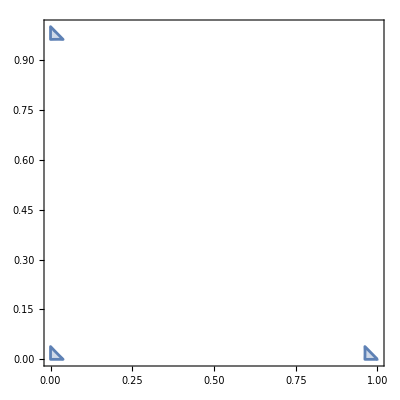

```mathematica
RegionPlot[Subscript[β, 1] Subscript[β, 2]+(Subscript[β, 1]+Subscript[β, 2])(1-Subscript[β, 1]-Subscript[β, 2])<1/27&&Subscript[β, 1]+Subscript[β, 2]<=1,{Subscript[β, 1],0,1},{Subscript[β, 2],0,1}]
```

### Radiation Reaction

The reason behind the waveform degeneracy at short time scales can be seen in the Taylor expansion of the phase of the systems.

```mathematica
Series[5^(3/8)/8 ℳ^(-5/8)(5/256×Subscript[a, 0]^4/(M^(4/3)ℳ^(5/3))-t)^(-3/8),{t,0,1}]//Simplify
```

1/(ℳ^(5/8) (a_0^4/(M^(4/3) ℳ^(5/3)))^(3/8))+(96 M^4 ℳ^(35/8) (a_0^4/(M^(4/3) ℳ^(5/3)))^(13/8) t)/(5 a_0^12)+O[t]^2

```mathematica
Series[-5^(-5/8)ℳ^(-5/8)(5/256×Subscript[a, 0]^4/(M^(4/3)ℳ^(5/3))-t)^(5/8),{t,0,2}]//FullSimplify
```

-((a_0^4/(M^(4/3) ℳ^(5/3)))^(5/8))/(32 ℳ^(5/8))+t/(ℳ^(5/8) (a_0^4/(M^(4/3) ℳ^(5/3)))^(3/8))+(48 M^4 ℳ^(35/8) (a_0^4/(M^(4/3) ℳ^(5/3)))^(13/8) t^2)/(5 a_0^12)+O[t]^3

```mathematica
3(Subscript[β, 1] Subscript[β, 2](Subscript[β, 1]-Subscript[β, 2])+Subscript[β, 2] Subscript[β, 3](Subscript[β, 2]-Subscript[β, 3])+Subscript[β, 1] Subscript[β, 3](Subscript[β, 3]-Subscript[β, 1]))^2+(Subscript[β, 1]-Subscript[β, 2])^2(Subscript[β, 1]-Subscript[β, 3])^2(Subscript[β, 2]-Subscript[β, 3])^2//FullSimplify
```

4 (β_1-β_2)^2 (β_1-β_3)^2 (β_2-β_3)^2

```mathematica
(Subscript[β, 2]-Subscript[β, 3])^2((Subscript[β, 1]-Subscript[β, 2])(Subscript[β, 1]-Subscript[β, 3])-3 Subscript[β, 2] Subscript[β, 3])^2+3 Subscript[β, 1]^2(Subscript[β, 2](Subscript[β, 2]-Subscript[β, 1])+Subscript[β, 3](Subscript[β, 1]-Subscript[β, 3]))^2//FullSimplify
```

(β_2-β_3)^2 (3 β_1^2 (-β_1+β_2+β_3)^2+(β_1^2-2 β_2 β_3-β_1 (β_2+β_3))^2)

The Lagrange three-body system coalesces first when . This simplifies to the following:

```mathematica
M(((Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 2] Subscript[β, 3])^2-3(Subscript[β, 1]^2 Subscript[β, 2] Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2]^2 Subscript[β, 3]+Subscript[β, 1] Subscript[β, 2] Subscript[β, 3]^2))/(Subscript[β, 1] Subscript[β, 2]+Subscript[β, 1] Subscript[β, 3]+Subscript[β, 2] Subscript[β, 3]))^(3/5)/.Subscript[β, 3]->1-Subscript[β, 1]-Subscript[β, 2]//FullSimplify
```

M (-β_1 (2+β_1)-(-1+β_1) β_2-β_2^2+(3 (-1+β_1) β_1^2)/(β_1^2+β_1 (-1+β_2)+(-1+β_2) β_2))^(3/5)

```mathematica
Manipulate[RegionPlot[{-1/(totalMass^(5/3) (Subscript[β, 1] (2+Subscript[β, 1])+(-1+Subscript[β, 1]) Subscript[β, 2]+Subscript[β, 2]^2-(3 (-1+Subscript[β, 1]) Subscript[β, 1]^2)/(Subscript[β, 1]^2+Subscript[β, 1] (-1+Subscript[β, 2])+(-1+Subscript[β, 2]) Subscript[β, 2])))<(Subscript[M, chirp][13.7, 7.7,0])^(-5/3)&&Subscript[β, 1]+Subscript[β, 2]<1,Subscript[β, 1] Subscript[β, 2]+(Subscript[β, 1]+Subscript[β, 2])(1-Subscript[β, 1]-Subscript[β, 2])<1/27&&Subscript[β, 1]+Subscript[β, 2]<=1},{Subscript[β, 1],0,1},{Subscript[β, 2],0,1},BoundaryStyle->Dashed,PlotLegends->{"t_(c, (3  B))<t_(c, (2  B))","Stable Region"}],{totalMass,0.1,200}]
```

```mathematica
oct1=A==4/r M^(5/3)ω^(2/3)Subscript[β, 1](1-3 Subscript[β, 1])Cos[ι];
oct2= B==(3 √3)/(4r)M^2 ω Subscript[β, 1](1-2 Subscript[β, 1])(1-3 Subscript[β, 1])Sin[2ι];
oct3= C==(9 √27)/(4r)M^2 ω Subscript[β, 1]^2(1-2 Subscript[β, 1])Sin[2ι];
```

```mathematica
SolveAlways[{oct2,oct3},{A,B,C,ω}]
```

{{M→0,r→0},{r→0,Sin[2 ι]→0},{r→0,β_1→0},{r→0,β_1→1/2}}

```mathematica
AbsoluteTiming[SolveAlways[{oct1,oct2},{A,B,C,ω}]]
```

$Aborted